# structure factor

### load data

```mathematica
p0s={3.85,3.825,3.80};
```

```mathematica
temperatures={{0.039 ,0.016, 0.01 ,0.005 ,0.00385, 0.0025 ,0.002, 0.001 ,0.0005 ,0.00033 ,0.00025, 0.00014, 0.000091,0.000077,0.000054, 0.000045, 0.000036},{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005},{0.063 ,0.039 ,0.03105, 0.025, 0.016 ,0.01 ,0.008 ,0.0063, 0.005, 0.00385, 0.0031, 0.0028 ,0.0025 ,0.0022}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate={{ 999999, 999999, 999999,999999, 999999,60, 80, 200, 500, 800, 999999, 999999, 999999,999999, 999999, 999999, 999999},{ 999999, 999999, 999999,999999, 999999,25, 40 ,60, 80, 120,200 ,300 ,1000 ,999999, 999999,999999},{ 999999, 999999, 999999,999999, 999999,40 ,70 ,150 ,250, 600 ,2000, 999999 ,999999, 999999},{ 999999, 999999, 999999,10 ,30 ,70, 150 ,700,1400, 999999 ,999999}};
```

```mathematica
tg={0.00007493513959359142,0.0005292353823088456,0.0021126581652639227,0.009308728608198327};
```

```mathematica
sks=Table[Table[Table[DeleteCases[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p","/scatteringFunction_N4096_p","_T","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],records[[p,i]]},{3,4,8,0,0}],"Data"],$Failed],{i,Length[records[[p]]]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
sks[[1,1,1]]
```

<|/k→NumericArray[…],/structureFactor→NumericArray[<380,808>, Real64],/time→NumericArray[…]|>

```mathematica
sksMean=Table[Table[Table[Mean[Flatten[Table[Table[sks[[p,T,i,2,time,k]],{time,Ceiling[Length[sks[[p,T,i,2]]]*4/5],Length[sks[[p,T,i,2]]]}],{i,Length[records[[p]]]}]]],{k,Length[sks[[p,T,1,1,1]]]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

$Aborted

```mathematica
sksMean23=Table[Table[Table[Mean[Flatten[Table[Table[sks[[p,T,i,2,time,k]],{time,Ceiling[Length[sks[[p,T,i,2]]]*2/3],Length[sks[[p,T,i,2]]]}],{i,Length[records[[p]]]}]]],{k,Length[sks[[p,T,1,1,1]]]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
sksMean1920=Table[Table[Table[Mean[Flatten[Table[Table[sks[[p,T,i,2,time,k]],{time,Ceiling[Length[sks[[p,T,i,2]]]*19/20],Length[sks[[p,T,i,2]]]}],{i,Length[records[[p]]]}]]],{k,Length[sks[[p,T,1,1,1]]]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
Length[sks[[1,1,1,1,1]]]
```

808

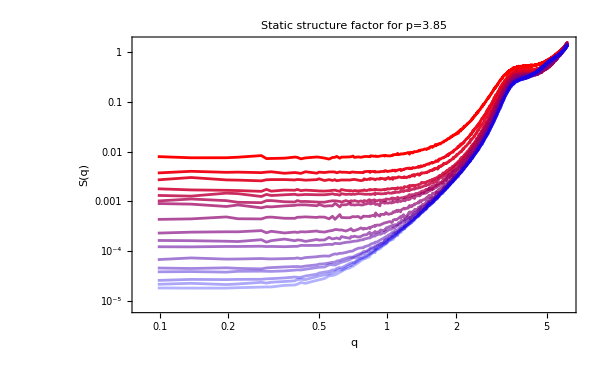
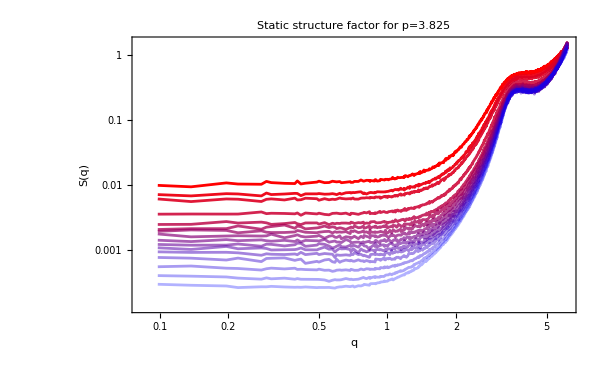
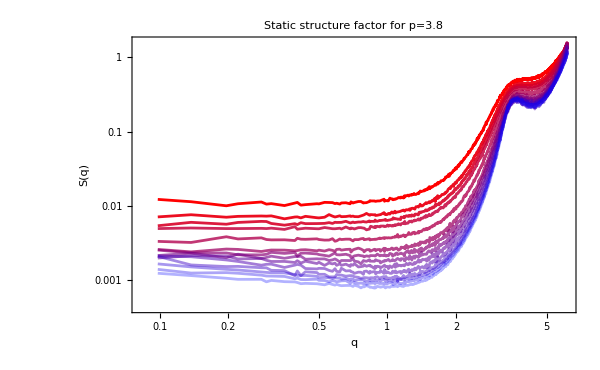

```mathematica
sqPLot=Table[ListLogLogPlot[Table[Table[{sks[[p,T,1,1,1,rec]],sksMean23[[p,T,rec]]},{rec,Length[sksMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],Joined->True,FrameLabel->{"q","S(q)"},PlotLabel->"Static structure factor for p="<>ToString[p0s[[p]]],ImageSize->600],{p,Length[p0s]}]
```

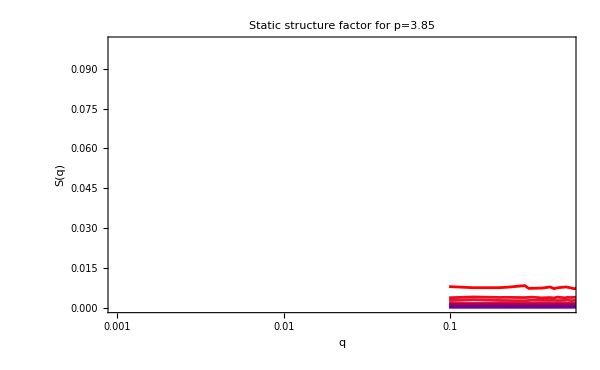
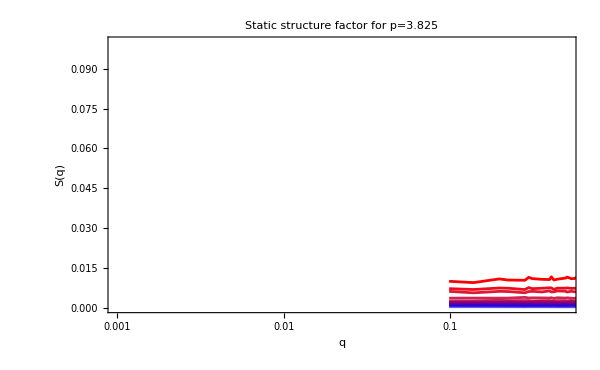
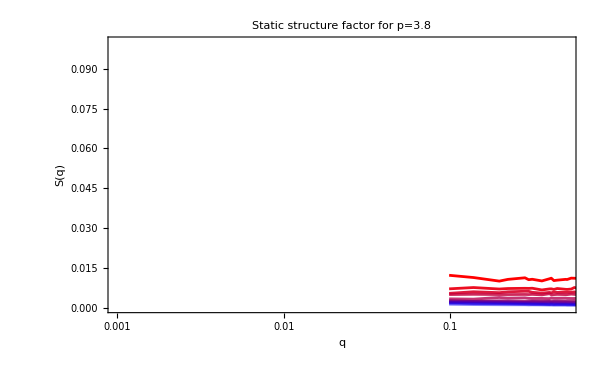

```mathematica
Table[ListLogLinearPlot[Table[Table[{sks[[p,T,1,1,1,rec]],sksMean23[[p,T,rec]]},{rec,Length[sksMean23[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotRange->{{0.001,0.5},{0.0001,0.1}},PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],Joined->True,FrameLabel->{"q","S(q)"},PlotLabel->"Static structure factor for p="<>ToString[p0s[[p]]],ImageSize->600],{p,Length[p0s]}]
```

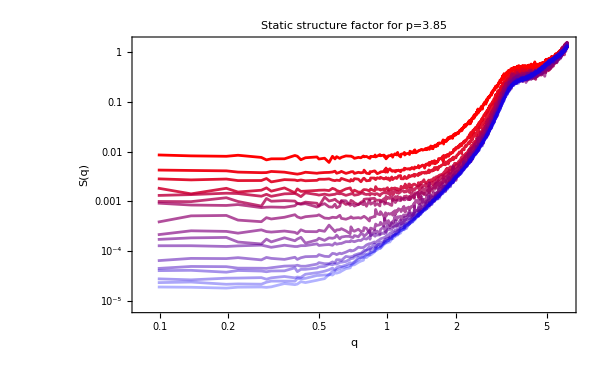
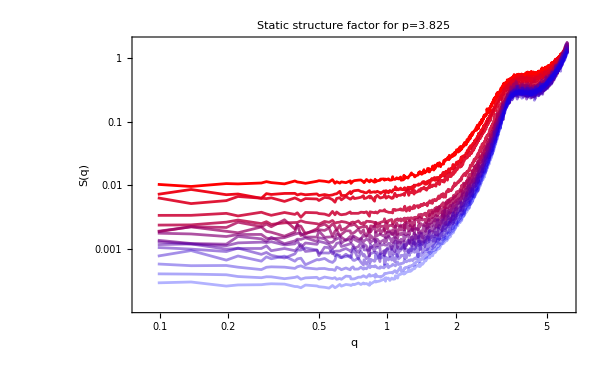
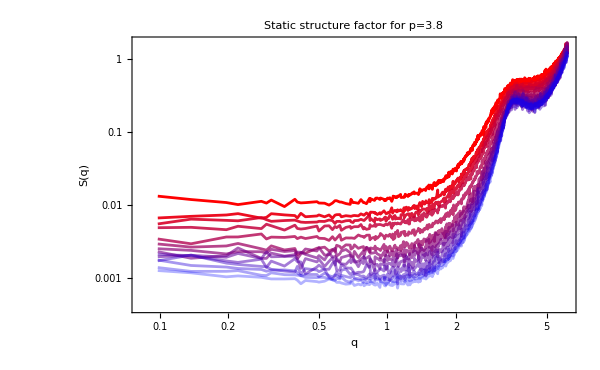

```mathematica
sq1920PLot=Table[ListLogLogPlot[Table[Table[{sks[[p,T,1,1,1,rec]],sksMean1920[[p,T,rec]]},{rec,Length[sksMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],Joined->True,FrameLabel->{"q","S(q)"},PlotLabel->"Static structure factor for p="<>ToString[p0s[[p]]],ImageSize->600],{p,Length[p0s]}]
```

```mathematica
sq23PLot=Table[ListLogLogPlot[Table[Table[{sks[[p,T,1,1,1,rec]],sksMean23[[p,T,rec]]},{rec,Length[sksMean23[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],Joined->True,FrameLabel->{"q","S(q)"},PlotLabel->"Static structure factor for p="<>ToString[p0s[[p]]],ImageSize->600],{p,Length[p0s]}]
```

{-Graphics-,-Graphics-,-Graphics-}

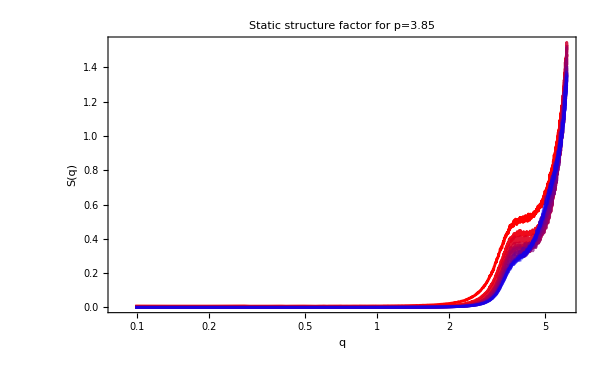
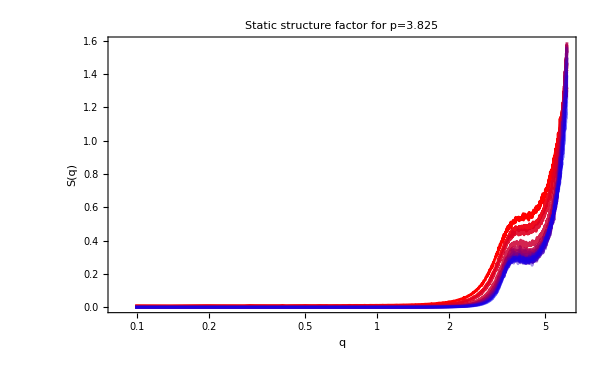
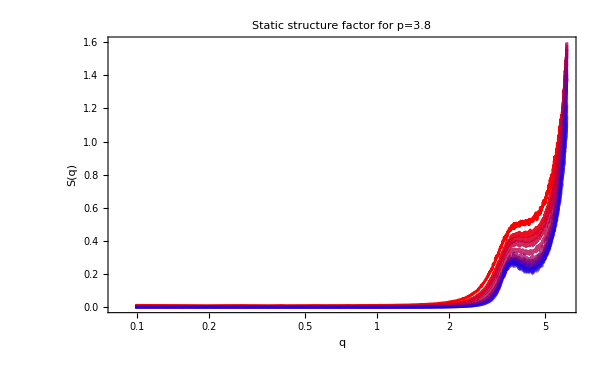

```mathematica
Table[ListLogLinearPlot[Table[Table[{sks[[p,T,1,1,1,rec]],sksMean23[[p,T,rec]]},{rec,Length[sksMean23[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],Joined->True,FrameLabel->{"q","S(q)"},PlotLabel->"Static structure factor for p="<>ToString[p0s[[p]]],ImageSize->600],{p,Length[p0s]}]
```

```mathematica
tshows={1,3,4,7,9,11,13,15,16};
tshowsInset={15,16,17};
```

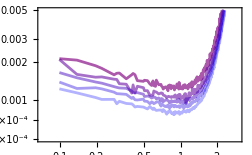

```mathematica
sqInset=Table[ListLogLogPlot[Table[Table[{sks[[p,T,1,1,1,rec]],sksMean23[[p,T,rec]]},{rec,Length[sksMean23[[p,T]]]}],{T,10,14}],PlotStyle->redBluePlotConfig[9][[5;;]],PlotRange->{{0.07,3},{0.0005,0.005}},Joined->True,(*FrameLabel->{"q","S(q)"},*)LabelStyle->Directive[FontSize->20,FontName->"Arial"],ImageSize->3.5*72.,ImageSize->8*72.],{p,3,3}]
```

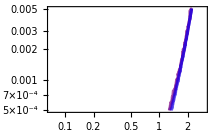

```mathematica
sqInset=Table[ListLogLogPlot[Table[Table[{sks[[p,T,1,1,1,rec]],sksMean23[[p,T,rec]]},{rec,Length[sksMean23[[p,T]]]}],{T,10,14}],PlotStyle->redBluePlotConfig[9][[5;;]],PlotRange->{{0.07,3},{0.0005,0.005}},Joined->True,FrameLabel->{"q","S(q)"},ImageSize->3*72.,LabelStyle->Directive[FontSize->12],ImageSize->8*72.],{p,1,1}]
```

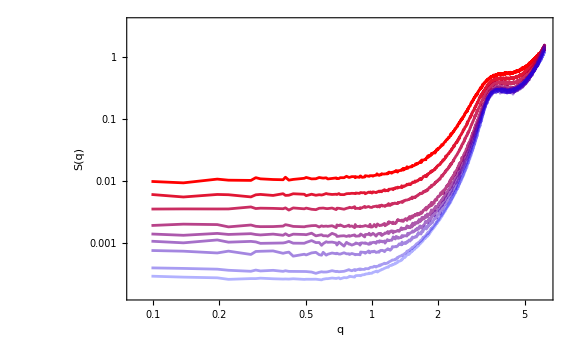

```mathematica
paperFigure1b=Table[ListLogLogPlot[Table[Table[{sks[[p,T,1,1,1,rec]],sksMean23[[p,T,rec]]},{rec,Length[sksMean23[[p,T]]]}],{T,tshows}],LabelStyle->Directive[FontSize->20,FontFamily->{"Arial"}],PlotStyle->redBluePlotConfig[Length[tshows]],PlotRange->{All,{0.00015,3.5}},Joined->True,FrameLabel->{"q","S(q)"},ImageSize->8*72.,Epilog->{Inset[sqInset[[1]],{-1.,-1.3},Automatic]}],{p,2,2}]
```

```mathematica
paperFigure1b[[1]]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/paperFigures/Sq.jpeg",paperFigure1b[[1]],ImageResolution->400]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/paperFigures/Sq.jpeg

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/paperFigures/tauGpTPLot.jpeg",gpTPlot,ImageResolution->400]
```

```mathematica
Export["/home/chengling/Research/updates/07282024/sqPLots.jpeg",Grid[Partition[Flatten[sq23PLot],1]],ImageResolution->300]
```

/home/chengling/Research/updates/07282024/sqPLots.jpeg

### Bulk Modulus

```mathematica
blueGraient=Flatten[Table[{RGBColor[0.5,0.7,1,0.6],RGBColor[0.3,0.5,0.8,0.6],RGBColor[0,0.1,0.5,0.6]},{i,4}]]
```

{RGBColor[0.5, 0.7, 1, 0.6],RGBColor[0.3, 0.5, 0.8, 0.6],RGBColor[0, 0.1, 0.5, 0.6],RGBColor[0.5, 0.7, 1, 0.6],RGBColor[0.3, 0.5, 0.8, 0.6],RGBColor[0, 0.1, 0.5, 0.6],RGBColor[0.5, 0.7, 1, 0.6],RGBColor[0.3, 0.5, 0.8, 0.6],RGBColor[0, 0.1, 0.5, 0.6],RGBColor[0.5, 0.7, 1, 0.6],RGBColor[0.3, 0.5, 0.8, 0.6],RGBColor[0, 0.1, 0.5, 0.6]}

```mathematica
bulkModulusArea={{1.968426434750778,1.9756648993762738,1.979838773012185,1.9855222999830129,1.9879326110813131,1.9910874587243015,1.9927199379385576,1.9965456337028877,1.9986500211935154,1.999344503211431,1.9995999457334805,1.9998561352942155,1.9999363204876823,1.999905204327633,1.999951443406994,1.9999610273428794,1.9999630396581765},{1.976367884068281,1.9727980102988816,1.9732216010769077,1.977677972587993,1.9795803998572856,1.9807289909325259,1.9819972163332469,1.9833329035080955,1.9846848080210482,1.9860097575020328,1.9869446262799315,1.987813425495713,1.9900504101170033,1.9911933587759232,1.992231344762208,1.9946860749765596},{1.970330901068985,1.973349664548752,1.975128481311054,1.9746938839173274,1.9773343100682998,1.9769706418157926,1.9756087174276613,1.9743256880910025,1.9721098005665507,1.9695250906164143,1.9682035386111305,1.9706529831885724,1.9743020829109141,1.9773259771928882}};
bulkModulusPeri={{3.1327868264012793,2.146669679594135,1.625445274825759,0.9613447767457817,0.7708497810237818,0.49584760259221594,0.3896030453314479,0.14924549774367601,0.045367576364034615,0.017862914323601802,0.013366041456455355,0.00727435539984978,0.008808819267151232,0.007044538150156038,0.008378659397645332,0.009381521318033909,0.004916821772182463},{3.9235712490701955,3.34492964624597,3.1090866508401844,2.394355999351477,1.81350140799965,1.5372789312579487,1.2562339007358252,1.0098889800876314,0.697893661877171,0.5144012690755295,0.31436160117244083,0.16183413459527374,0.05992257043973409,-0.1895833548666876,-0.37799115694107793,-0.2784861412942186},{3.9845466836681,3.5530111069355526,3.3680861484574054,3.092336863122748,2.56849555108396,1.7945904545591598,1.3708111421703097,0.8165136813594182,0.28331545146936116,-0.23555257510001448,-0.5267191387567112,-0.4094907539634249,-0.23833051629748753,-0.1305220947298187}};
```

```mathematica
bulkModulusNumerical=bulkModulusArea+bulkModulusPeri
```

{{5.10121,4.12233,3.60528,2.94687,2.75878,2.48694,2.38232,2.14579,2.04402,2.01721,2.01297,2.00713,2.00875,2.00695,2.00833,2.00934,2.00488},{5.89994,5.31773,5.08231,4.37203,3.79308,3.51801,3.23823,2.99322,2.68258,2.50041,2.30131,2.14965,2.04997,1.80161,1.61424,1.7162},{5.95488,5.52636,5.34321,5.06703,4.54583,3.77156,3.34642,2.79084,2.25543,1.73397,1.44148,1.56116,1.73597,1.8468}}

```mathematica
averageRange={{21,21,21,21,21,21,21,21,14,14,14,4,4,4,4,4,4},{21,21,21,21,21,21,21,21,5,10,5,5,5,5,5,5},{22,22,22,22,10,1,1,1,2,1,1,1,1,1}};
```

```mathematica
compressibility=Table[Table[Mean[Table[sksMean[[p,T,rec]],{rec,averageRange[[p,T]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.00754354,0.00383716,0.00270329,0.00165669,0.00137876,0.000998555,0.00083079,0.000476877,0.000244207,0.000164931,0.000127144,0.0000699593,0.0000451033,0.000039347,0.0000268876,0.0000222386,0.0000184099},{0.0109946,0.00728612,0.00604125,0.0036012,0.00256844,0.00222342,0.00193737,0.00164763,0.00142422,0.00121297,0.00107852,0.000914532,0.00074898,0.000530692,0.000378899,0.000279455},{0.0108344,0.00714431,0.00587936,0.00499022,0.00349219,0.00262634,0.0023939,0.00216442,0.00210351,0.00215175,0.00191636,0.00167229,0.00141524,0.0011898}}

```mathematica
compressibility={{0.0075435405198725665,0.003837158848808109,0.0027032909802595963,0.0016566948787492617,0.0013787595324467933,0.0009985550639928114,0.0008307897778321875,0.0004768767345449935,0.0002442072481156129,0.00016493121832944878,0.00012714368346567227,0.00006995927957803198,0.00004510331885851859,0.000039347024692661294,0.00002688758284510201,0.000022238613337757643,0.00001840989687089748},{0.010994617647207203,0.007286121275593245,0.00604124861958744,0.0036012048156658628,0.002568438601783545,0.002223416769814999,0.001937371878834571,0.0016476259965166643,0.0014242163889660266,0.0012129712675893625,0.0010785236691362968,0.0009145321317645535,0.000748980109113872,0.000530691662565797,0.00037889872707835116,0.0002794551877747317},{0.010834389998469288,0.007144312416283938,0.005879359367864972,0.004990222464737518,0.00349219138547503,0.002626339080442435,0.002393895054369465,0.002164417014298292,0.00210350696752443,0.0021517472096229525,0.0019163569638352266,0.0016722941007749244,0.0014152389263074575,0.0011897966486779544}};
```

```mathematica
kS=Table[Table[1/(compressibility[[p,T]]/temperatures[[p,T]]),{T,Length[temperatures[[p]]]}],{p,3}]
```

{{5.16999,4.16975,3.69919,3.01806,2.79237,2.50362,2.40735,2.09698,2.04744,2.00083,1.96628,2.00116,2.01759,1.95695,2.00836,2.02351,1.95547},{5.73008,5.35264,5.13967,4.44296,3.89342,3.59807,3.25183,3.03467,2.70324,2.55571,2.31798,2.18691,2.00272,1.88433,1.76828,1.7892},{5.81482,5.45889,5.28119,5.0098,4.58165,3.80758,3.34183,2.91071,2.37698,1.78924,1.61765,1.67435,1.76649,1.84906}}

```mathematica
compressibilityTest=Table[Table[Mean[Table[sksMean910[[p,T,rec]],{rec,7}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.00763334,0.0038593,0.0027341,0.00168063,0.00134953,0.00102316,0.000820481,0.000462041,0.000245042,0.000161771,0.000124768,0.0000707012,0.0000460094,0.0000393788,0.0000274303,0.0000227939,0.000018796},{0.0104579,0.00716959,0.00595207,0.00364103,0.00258583,0.00218882,0.00193397,0.0016728,0.00139837,0.00120345,0.00105907,0.000892121,0.00073065,0.000527311,0.000376816,0.000277378},{0.0109428,0.0072371,0.00585746,0.00495129,0.00350853,0.00251177,0.00229699,0.00209787,0.00195279,0.00180461,0.00156742,0.00138395,0.00121775,0.00105613}}

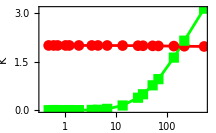

```mathematica
inset=Table[ListLogLinearPlot[{Table[{temperatures[[p,T]]/tg[[p]],bulkModulusArea[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]]/tg[[p]],bulkModulusPeri[[p,T]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"T","K"},ImageSize->3*72.,LabelStyle->Directive[FontSize->20],PlotMarkers->Automatic,PlotStyle->{Red,Green},Joined->True],{p,1,1}]
```

```mathematica
openHexagon=Graphics[{EdgeForm[{Blue,Thickness[0.03]}],FaceForm[None],Polygon[Table[{Cos[θ],Sin[θ]},{θ,0,2 π,π/3}]]},PlotRange->{{-1,1},{-1,1}},AspectRatio->1,Background->Transparent,ImageSize->20]
```

-Graphics-

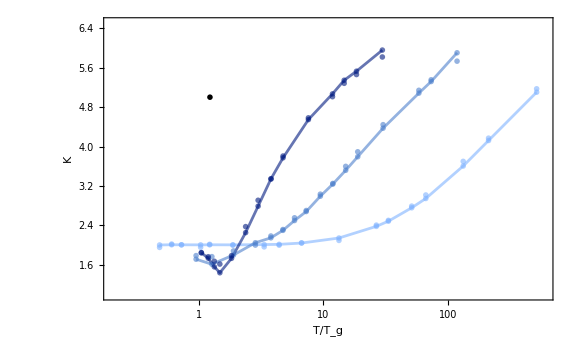

```mathematica
modulusPlot=Show[ListLogLinearPlot[Table[Table[{temperatures[[p,T]]/tg[[p]],bulkModulusNumerical[[p,T]]},{T,Length[bulkModulusNumerical[[p]]]}],{p,Length[p0s]}],LabelStyle->Directive[FontSize->20],FrameLabel->{"T/T_g","K"},ImageSize->8*72.,(*PlotLabel->"K obtained by static structure factor and numerical compression vs T/T_g",*)PlotMarkers->pm1[6,blueGraient],PlotStyle->blueGraient,PlotRange->{{0.2,600},{1,6.5}},PlotLegends->{"K_N p_0=3.85","K_N p_0=3.825","K_N p_0=3.80"},Joined->True,Epilog->{Inset[inset[[1]],{0.2,5},Automatic]}],ListLogLinearPlot[Table[Table[{temperatures[[p,T]]/tg[[p]],1/(compressibility[[p,T]]/temperatures[[p,T]])},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],LabelStyle->Directive[FontSize->20],FrameLabel->{"T","K"},ImageSize->600,PlotLabel->"K vs T/T_g",PlotMarkers->pm2[6,blueGraient],PlotStyle->blueGraient,PlotLegends->{"K_s p_0=3.85","K_s p_0=3.825","K_s p_0=3.80"},Joined->False](*ListLogLinearPlot[Table[Table[{temperatures[[p,T]]/tg[[p]],bulkModulusNumerical[[p,T]]},{T,Length[temperatures[[p]]]-{8,1,3}[[p]],Length[temperatures[[p]]]}],{p,2,3}],FrameLabel->{"G_p/T ","tau"},ImageSize->600,PlotMarkers->{openHexagon,0.07},PlotLabel->"tau vs G_p/T",PlotLegends->{"hexatic phase"},PlotRange->{{2,14},All},Joined->False]*)]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/paperFigures/bulkModulusPlot.jpeg",modulusPlot,ImageResolution->400]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/paperFigures/bulkModulusPlot.jpeg